```mathematica
sigmoid[x_]=1/(1+Exp[-x]);
```

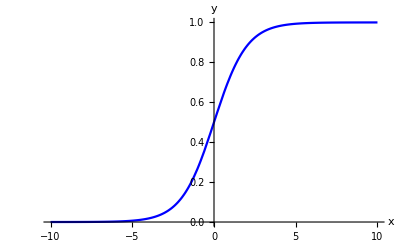

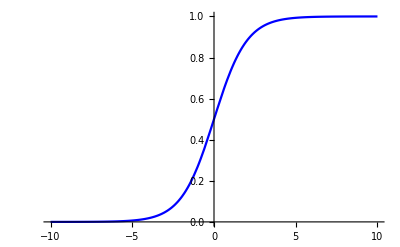

```mathematica
Plot[sigmoid[x],{x,-10,10}, PlotRange->Full, AxesLabel->{Text[Style[x,Large]],Text[Style[y,Large]]},PlotStyle->Blue]
sig=Plot[sigmoid[x],{x,-10,10}, PlotRange->Full, PlotStyle->Blue,AxesStyle->Black,TicksStyle->Black]
```

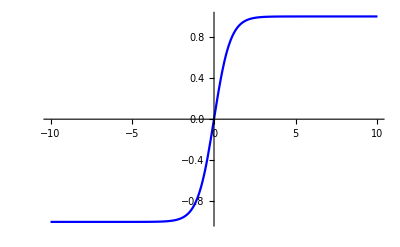

```mathematica
tanh=Plot[Tanh[x],{x,-10,10}, PlotRange->Full, PlotStyle->Blue,AxesStyle->Black,TicksStyle->Black]
```

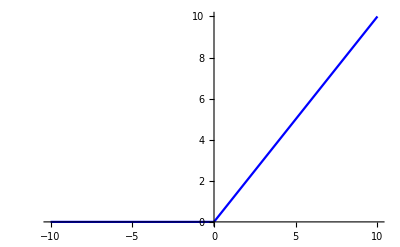

```mathematica
relu=Plot[Piecewise[{{0,x<0},{x,x≥ 0}}],{x,-10,10}, PlotRange->Full, PlotStyle->Blue,AxesStyle->Black,TicksStyle->Black]
(*relu=Plot[Piecewise[{{0,x<0},{x,x≥ 0}}],{x,-10,10}, PlotRange->Full, PlotStyle->Blue,AxesStyle->Black,TicksStyle->Black,GridLines->Automatic]*)
```

```mathematica
Export[NotebookDirectory[]<>"sig"<>".png",sig,ImageResolution->150];
```

```mathematica
Export[NotebookDirectory[]<>"tanh"<>".png",tanh,ImageResolution->150];
```

```mathematica
Export[NotebookDirectory[]<>"relu"<>".png",relu,ImageResolution->150];
```

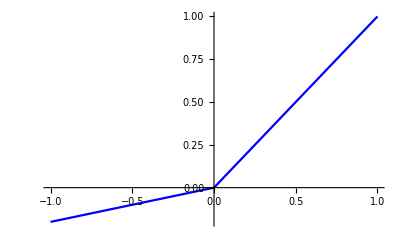

```mathematica
prerelu=Plot[Piecewise[{{0.2x,x<0},{x,x≥ 0}}],{x,-1,1}, PlotStyle->Blue,AxesStyle->Black,TicksStyle->Black]
```

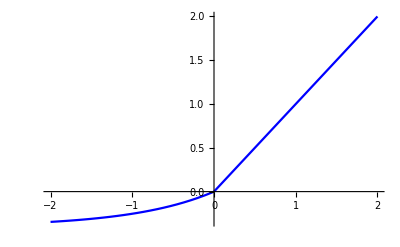

```mathematica
elu=Plot[Piecewise[{{0.4(Exp[x]-1),x<0},{x,x≥ 0}}],{x,-2,2}, PlotStyle->Blue,AxesStyle->Black,TicksStyle->Black]
```

```mathematica
Export[NotebookDirectory[]<>"prerelu"<>".png",prerelu,ImageResolution->150];
```

```mathematica
Export[NotebookDirectory[]<>"elu"<>".png",elu,ImageResolution->150];
```